

```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
Manipulate[
Plot[x^3+α x^2+β x,{x,-2,2}]
,{{α,0},-1,1},{{β,0},-1,1}]
```

```mathematica
Manipulate[
Plot[x^3+α x^2+β x,{x,-2,2},PlotRange->{{-2,2},{-2,2}}]
,{{α,0},-1,1},{{β,0},-1,1}]
```

```mathematica
Manipulate[
Plot[{x^3+α x^2+β x,x^3,x^2,x}
,{x,-2,2},PlotRange->{{-2,2},{-2,2}},PlotLegends->"Expressions"]
,{{α,0},-1,1},{{β,0},-1,1}]
```

```mathematica
{x^3,x^2,x}/(Total@{x^3,x^2,x})
```

{x^3/(x+x^2+x^3),x^2/(x+x^2+x^3),x/(x+x^2+x^3)}

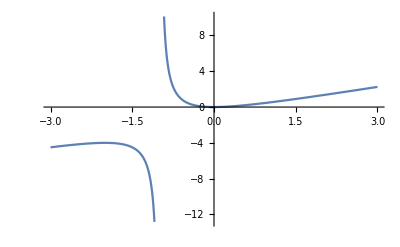

```mathematica
Plot[x^2/(1+x),{x,-3,3}]
```

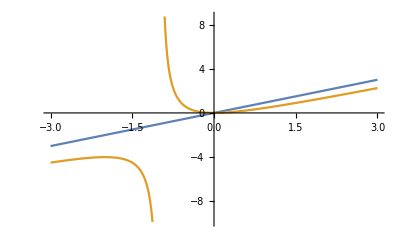

```mathematica
Plot[{x,x^2/(1+x)},{x,-3,3}]
```

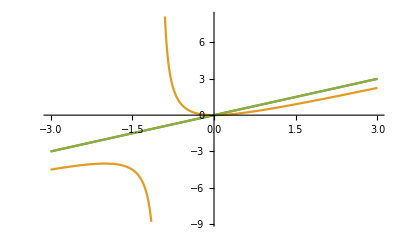

```mathematica
Plot[{x,x^2/(1+x),x^2/(1+(x-1))},{x,-3,3}]
```

```mathematica
√(x^2+1)-√(x^2-1)
```

-√(-1+x^2)+√(1+x^2)

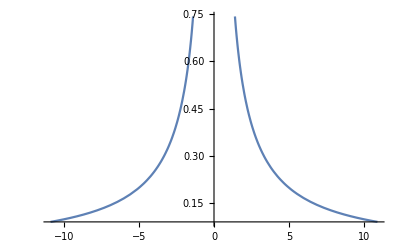

```mathematica
Plot[-√(-1+x^2)+√(1+x^2),{x,-10.92,10.92}]
```

```mathematica
√(x^2+1)
```

√(1+x^2)

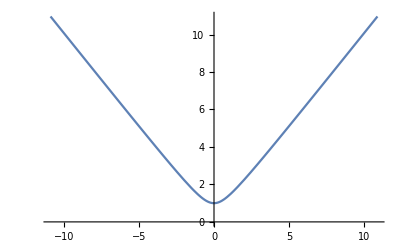

```mathematica
Plot[√(1+x^2),{x,-10.92,10.92}]
```

```mathematica
Dt[S==x^2+y^2]
```

Dt[S]==2 x Dt[x]+2 y Dt[y]

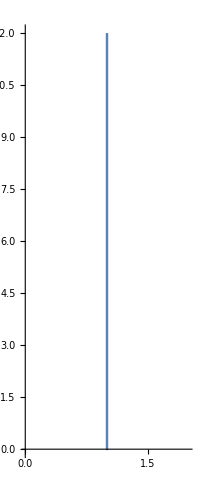

```mathematica
ParametricPlot[{1,3 x^2},{x,-2,2}]
```

```mathematica
StreamPlot[{x,3 x^2},{x,y}∈Reals]
```

StreamPlot::idomdim: {x,y}∈ does not have a valid dimension as a plotting domain.

StreamPlot[{x,3 x^2},{x,y}∈ℝ]

```mathematica
StreamPlot[{x,3 x^2},{x,y}∈Reals^2]
```

StreamPlot::idomdim: {x,y}∈^2 does not have a valid dimension as a plotting domain.

StreamPlot[{x,3 x^2},{x,y}∈ℝ^2]

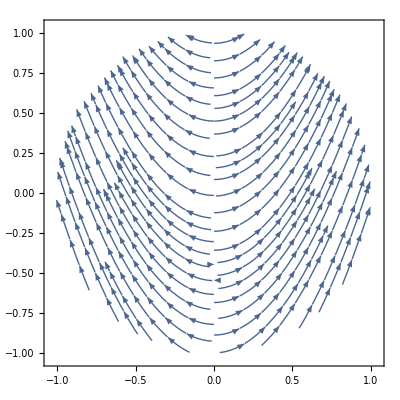

```mathematica
StreamPlot[{x,3 x^2},{x,y}∈Disk[]]
```

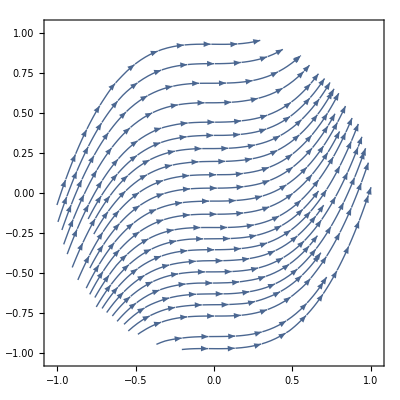

```mathematica
StreamPlot[{1,3 x^2},{x,y}∈Disk[]]
```

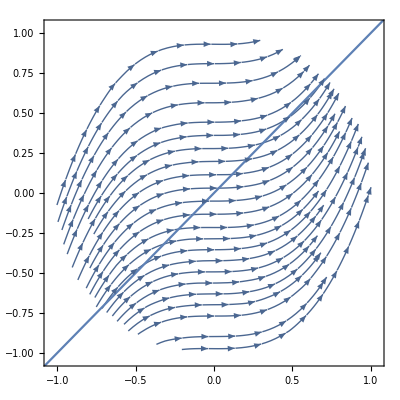

```mathematica
Show[{StreamPlot[{1,3 x^2},{x,y}∈Disk[]],Plot[x,{x,-2,2}]}]
```

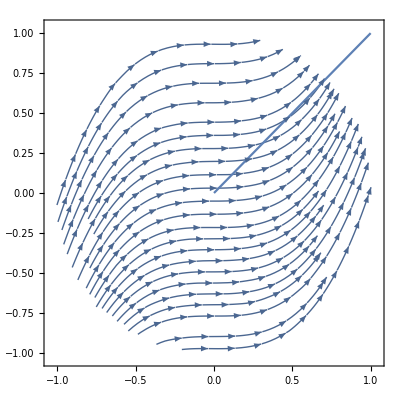

```mathematica
Show[{StreamPlot[{1,3 x^2},{x,y}∈Disk[]],Plot[x,{x,0,1}]}]
```

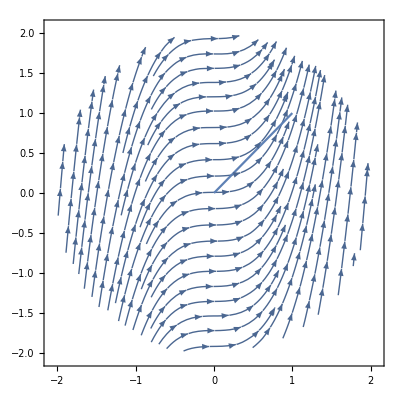

```mathematica
Show[{StreamPlot[{1,3 x^2},{x,y}∈Disk[{0,0},2]],Plot[x,{x,0,1}]}]
```

```mathematica
Show[{StreamPlot[{1,3 x^2},{x,y}∈Disk[{0,0},2]],Plot[x,{x,0,1}]}]
```

```mathematica
{1,3 x^2}/.x->t
```

{1,3 t^2}

```mathematica
Integrate[{1,3 t^2},{t,0,1}]
```

{1,1}

```mathematica
Integrate[{1,3 t^2},t]
```

{t,t^3}

```mathematica
Integrate[3 x^2,x]
```

x^3

```mathematica
Integrate[3 x^2,{x,0,1}]
```

1